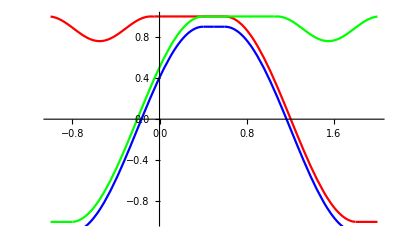

```mathematica
f[x_]:=Piecewise[{{0.88+0.12*Sin[(x-Pi/2)/0.150],x<-0.05},{1,x≤0.6},{Sin[(x-0.6)*2.6+Pi/2],0.6<x<1.8},{-1,1.8<x≤2}}];(*猜测函数*)
plot1=Plot[f[x],{x,-1,2},PlotStyle->Red];
g:=Piecewise[{{f[1-x],x<0.5},{f[x],x≥0.5}}];
plot2=Plot[f[1-x],{x,-1,2},PlotStyle->Green];
plot3=Plot[g-0.1,{x,-1,2},PlotStyle->Blue];
Show[plot1,plot2,plot3]
```